# Simple Circuits

Figure of a single loop with a Resistor (V=i R) a Capacitor (V=q/C) and a voltage source  E(t) connected in a single loop.

Equation pieces
q(t) 			....	charge on the capacitor
i(t)=q'(t) 	.... 	rate of change of charge on the capacitor
C and R 		.... 	parameter values read of the components
E(t)			....	Voltage source chosen from various possibilities.

Equation
Words	...	Voltages sum to zero round a loop
Symbols 	...	V_c+V_r+E(t)=0

Component Voltages
V_r=i R
V_c = q/C

ODE
q(t)/C + q'(t) R+E(t)=0

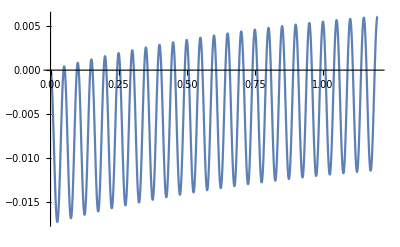

```mathematica
{CVal, RVal}={0.01,100};
VoltageSource[t_]:=110Sin[2π (t 20)]
TMax=1.2;
qSol=NDSolveValue[
{q[t]/CVal+q'[t] RVal + VoltageSource[t]==0, q[0]==0},q,{t, 0, TMax}];
Plot[qSol[t],{t, 0, TMax}]
```

```mathematica
SawtoothWave
```

SawtoothWave

```mathematica
Information[SawtoothWave]
```

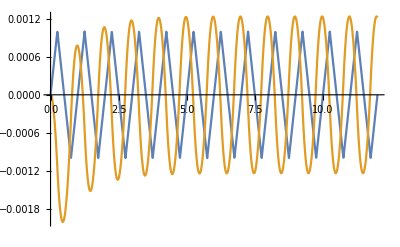

```mathematica
{CVal, RVal}={0.01,100};
VoltageSource[t_]:=TriangleWave[t]
TMax=12;
qSol=NDSolveValue[
{q[t]/CVal+q'[t] RVal + VoltageSource[t]==0, q[0]==0},q,{t, 0, TMax}];
Plot[{0.001VoltageSource[t], qSol[t]},{t, 0, TMax}]
```

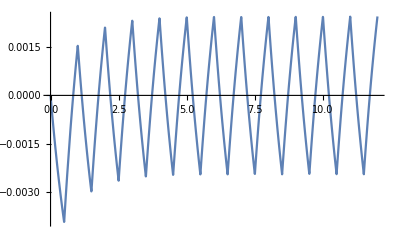

```mathematica
{CVal, RVal}={0.01,100};
VoltageSource[t_]:=SquareWave[t]
TMax=12;
qSol=NDSolveValue[
{q[t]/CVal+q'[t] RVal + VoltageSource[t]==0, q[0]==0},q,{t, 0, TMax}];
Plot[qSol[t],{t, 0, TMax}]
```

```mathematica
{CVal, RVal}={0.01,100};
VoltageSource[t_]:=TriangleWave[0.05t]
TMax=43;
qSol=NDSolveValue[
{q[t]/CVal+q'[t] RVal + VoltageSource[t]==0, q[0]==0},q,{t, 0, TMax}];
TabView[{
"q"->Plot[qSol[t],{t, 0, TMax}],
"E(t)"->Plot[VoltageSource[t],{t, 0, TMax}],
"i=q'(t)"->Plot[qSol'[t],{t, 0, TMax},PlotRange->All]}]
```

123

## Dumping Data

C:\Users\struther\Desktop

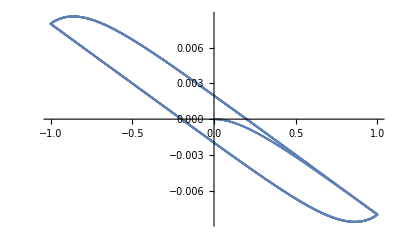

```mathematica
SetDirectory["C:\\Users\\struther\\Desktop"]
Data=Table[{VoltageSource[t],qSol[t]},{t,0, TMax,0.01}];
Export["AASData.csv",Data];
NewData=Import["AASData.csv"];
ListPlot[NewData[[All]]]
```